```mathematica
n = 2;
f[β_] :=1/(n+1) (Gamma[n+2] - Gamma[n+2, β])/(Gamma[n+1] - Gamma[n+1, β]);
```

```mathematica
f2[β_] := 1/n(ⅇ^-β β^(1+n)+(β-n) (Gamma[1+n]-Gamma[1+n,β]))/(β (Gamma[n]-Gamma[n,β]));
```

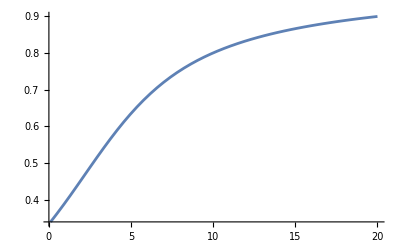

```mathematica
Plot[f2[β], {β, 0.1, 20}]
```

```mathematica
Limit[f2[β], β -> 0]
```

1/3

```mathematica
num[β_] := Sum[(β^k (k+1))/((m+k+1)!), {k, 0, Infinity}]
den[β_] := Sum[β^k/((m+k)!), {k, 0, Infinity}]
```

```mathematica
FullSimplify[num[β], Assumptions->{Element[m, Integers]}]
```

(β^(-1-m) (β^(1+m)+ⅇ^β (-m+β) (Gamma[1+m]-Gamma[1+m,β])))/Gamma[1+m]

```mathematica
FullSimplify[den[β], Assumptions->{Element[m, Integers]}]
```

(ⅇ^β β^-m (Gamma[m]-Gamma[m,β]))/Gamma[m]

```mathematica
FullSimplify[num[β] / den[β], Assumptions->{Element[m, Integers]}]
```

(ⅇ^-β Gamma[m] (β^(1+m)+ⅇ^β (-m+β) (Gamma[1+m]-Gamma[1+m,β])))/(β Gamma[1+m] (Gamma[m]-Gamma[m,β]))

```mathematica
FullSimplify[(num[β]/den[β] /. {m -> n}) == f2[β], Assumptions->{Element[m, Integers]}]
```

True